## 2 nd order without coupling

```mathematica
alpha0=5;
beta=1;
gama=0;
Tc1=2;
Tc2=5;
```

```mathematica
alpha1[t_]:=alpha0*(t-Tc1)
alpha2[t_]:=alpha0*(t-Tc2)
```

```mathematica
Fnorm[t_,psi1_,psi2_]:=alpha1[t]*psi1^2 + alpha2[t]*psi2^2+beta/2*(psi1^4+psi2^4)+gama/3*psi2^6
```

```mathematica
Manipulate[
Column[
{ContourPlot[Fnorm[t,psi1,psi2],{psi1,-8,8},{psi2,-8,8},Contours->30],
NMinimize[{Fnorm[t,psi1,psi2],0.<psi1<8,0.<psi2<8},{psi1,psi2}]}],
{{t,0},0,1.1 Tc2,.1}
]
```

## 2 nd order with coupling

```mathematica
alpha0=5;
beta=1;
gama=0;
Tc1=2;
Tc2=5;
v=0.4;
```

```mathematica
alpha1[t_]:=alpha0*(t-Tc1)
alpha2[t_]:=alpha0*(t-Tc2)
```

```mathematica
Fnorm2[t_,psi1_,psi2_]:=alpha1[t]*psi1^2 + alpha2[t]*psi2^2+beta/2*(psi1^4+psi2^4)+gama/3*psi2^6+v psi1^2 psi2^2
```

```mathematica
Manipulate[
Column[
{ContourPlot[Fnorm2[t,psi1,psi2],{psi1,-8,8},{psi2,-8,8},Contours->30],
NMinimize[{Fnorm2[t,psi1,psi2],0.<psi1<8,0.<psi2<8},{psi1,psi2}]}],
{{t,0},0,1.1 Tc2,.1}
]
```

NMinimize::ubnd: The problem is unbounded.

## other

```mathematica
dfdpsi1norm=D[Fnorm[t,psi1,psi2],psi1]
```

2 beta psi1^3+2 alpha0 psi1 (t-Tc1)

```mathematica
dfdpsi2norm=D[Fnorm[t,psi1,psi2],psi2]
```

2 beta psi2^3+2 gama psi2^5+2 alpha0 psi2 (t-Tc2)

```mathematica
psi1exts=Solve[dfdpsi1norm==0,psi1]
psi2exts=Solve[dfdpsi2norm==0,psi2]
```

{{psi1→0},{psi1→-(√(-alpha0 t+alpha0 Tc1))/(√beta)},{psi1→(√(-alpha0 t+alpha0 Tc1))/(√beta)}}

{{psi2→0},{psi2→-(√(-beta/gama-(√(beta^2-4 alpha0 gama t+4 alpha0 gama Tc2))/gama))/(√2)},{psi2→(√(-beta/gama-(√(beta^2-4 alpha0 gama t+4 alpha0 gama Tc2))/gama))/(√2)},{psi2→-(√(-beta/gama+(√(beta^2-4 alpha0 gama t+4 alpha0 gama Tc2))/gama))/(√2)},{psi2→(√(-beta/gama+(√(beta^2-4 alpha0 gama t+4 alpha0 gama Tc2))/gama))/(√2)}}

```mathematica
psi1norm=Last[Last[psi1exts[[3]]]]
```

(√(-alpha0 t+alpha0 Tc1))/(√beta)

```mathematica
psi2norm1=Last[Last[psi2exts[[3]]]]
```

(√(-beta/gama-(√(beta^2-4 alpha0 gama t+4 alpha0 gama Tc2))/gama))/(√2)

```mathematica
Fcop[t_,psi1_,psi2_]:=Fnorm[t,psi1,psi2]+v(psi1*psi2)^2
```

```mathematica
dfdpsi1cop=D[Fcop[t,psi1,psi2],psi1]
dfdpsi2cop=D[Fcop[t,psi1,psi2],psi2]
```

2 beta psi1^3+2 alpha0 psi1 (t-Tc1)+2 psi1 psi2^2 v

2 beta psi2^3+2 gama psi2^5+2 alpha0 psi2 (t-Tc2)+2 psi1^2 psi2 v

```mathematica
psi1exts1=Solve[dfdpsi1cop==0,psi1] //FullSimplify
psi1exts2=Solve[dfdpsi2cop==0,psi1]//FullSimplify
```

{{psi1→0},{psi1→-(√(alpha0 (-t+Tc1)-psi2^2 v))/(√beta)},{psi1→(√(alpha0 (-t+Tc1)-psi2^2 v))/(√beta)}}

{{psi1→-(√(-psi2^2 (beta+gama psi2^2)+alpha0 (-t+Tc2)))/(√v)},{psi1→(√(-psi2^2 (beta+gama psi2^2)+alpha0 (-t+Tc2)))/(√v)}}

```mathematica
psi1ext1cop=Last[Last[psi1exts1[[3]]]] //FullSimplify
```

(√(alpha0 (-t+Tc1)-psi2^2 v))/(√beta)

```mathematica
psi1ext2cop=Last[Last[psi1exts2[[2]]]]//FullSimplify
```

(√(-psi2^2 (beta+gama psi2^2)+alpha0 (-t+Tc2)))/(√v)

```mathematica
psi2cops=Solve [psi1ext1cop==psi1ext2cop,psi2] //FullSimplify
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{psi2→-(√((v^2-beta (beta+√((beta^4+4 alpha0 beta gama (t-Tc1) v+v^4-2 beta^2 (2 alpha0 gama (t-Tc2)+v^2))/beta^2)))/(beta gama)))/(√2)},{psi2→(√((v^2-beta (beta+√((beta^4+4 alpha0 beta gama (t-Tc1) v+v^4-2 beta^2 (2 alpha0 gama (t-Tc2)+v^2))/beta^2)))/(beta gama)))/(√2)},{psi2→-(√((-beta^2+v^2+beta √((beta^4+4 alpha0 beta gama (t-Tc1) v+v^4-2 beta^2 (2 alpha0 gama (t-Tc2)+v^2))/beta^2))/(beta gama)))/(√2)},{psi2→(√((-beta^2+v^2+beta √((beta^4+4 alpha0 beta gama (t-Tc1) v+v^4-2 beta^2 (2 alpha0 gama (t-Tc2)+v^2))/beta^2))/(beta gama)))/(√2)}}

```mathematica
psi2cop1=Last[Last[psi2cops[[2]]]] //FullSimplify
psi2cop2=Last[Last[psi2cops[[4]]]] //FullSimplify
```

(√((v^2-beta (beta+√((beta^4+4 alpha0 beta gama (t-Tc1) v+v^4-2 beta^2 (2 alpha0 gama (t-Tc2)+v^2))/beta^2)))/(beta gama)))/(√2)

(√((-beta^2+v^2+beta √((beta^4+4 alpha0 beta gama (t-Tc1) v+v^4-2 beta^2 (2 alpha0 gama (t-Tc2)+v^2))/beta^2))/(beta gama)))/(√2)

```mathematica
Replacepsi2:={psi2->psi2cop1}
psi1cop1=psi1ext1cop /.Replacepsi2//FullSimplify
psi1cop2=psi1ext2cop /.Replacepsi2 //FullSimplify
```

1/(√beta)(√(alpha0 (-t+Tc1)-(v (v^2-beta (beta+√((beta^4+4 alpha0 beta gama (t-Tc1) v+v^4-2 beta^2 (2 alpha0 gama (t-Tc2)+v^2))/beta^2))))/(2 beta gama)))

1/(√2 √v)(√(1/(beta^2 gama)v (2 alpha0 beta gama (-t+Tc1)+beta^2 v-v^3+beta v √(beta^2+4 alpha0 gama (-t+Tc2)+(4 alpha0 gama (t-Tc1) v)/beta-2 v^2+v^4/beta^2))))

```mathematica
alpha0=5;
beta=-1;
gama=1;
v=10;
Tc1=10;
Tc2=30;
```

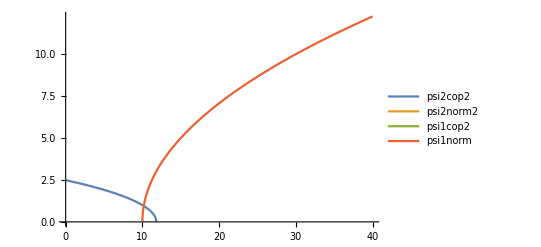

```mathematica
Plot[{psi2cop2,psi2norm2,psi1cop2,psi1norm},{t,0,40},PlotLegends->{"psi2cop2","psi2norm2","psi1cop2","psi1norm"}]
```

```mathematica
00
```

0

NMinimize::nnum: The function value -10 psi1^2-25 psi2^2-0.4 psi1^2 psi2^2+1/2 (psi1^4+psi2^4) is not a number at {x,y} = {-0.0813788,0.690102}.